# Solar wind discontinuities and ion scattering

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<utilities.wl
```

```mathematica
(*(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->Large}]*)
(*SetOptions[ParametricPlot3D,AxesStyle->Large];*)
(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->{}}]*)*)
```

```mathematica
On[Assert];
notationRules=Join[
{xN->x,zN->z},
{pxN->Subscript[p, x],pzN->Subscript[p, z]},
{px->Subscript[p, x],py->Subscript[p, y],pz->Subscript[p, z]}
];
formRules=notationRules;
assums={c>0,q>0,L>0,B0>0};
```

## Introduction

## Theoretical Analysis

Notation α=ρ/L

## Deduction

```mathematica
By[z_]:= Cos[β ArcTan[z]]
By[z_]:= Cos[β z/(√(1+z^2))]
Bx[z_]:= B0 Sin[α] Sin[β Tanh[z/L]]
By[z_]:= B0 Sin[α] Cos[β Tanh[z/L]]
Bz:=B0 Cos[α]
Ax:=Integrate[By[z],z]
Ay:=Integrate[-Bx[z],z]+ Integrate[Bz,x]
Az:=0
```

```mathematica
vecA:= {Ax,Ay,Az}
vecP={px,py,pz};
vecV=vecP-(q vecA)/c;vecA{x,y,z}//FullSimplify
```

{B0 Sin[α] Sin[β Tanh[z/L]],B0 Cos[β Tanh[z/L]] Sin[α],B0 Cos[α]}

```mathematica
n=2;(*order*)
Asymptotic[Bx[z],{z,0,n}]
Asymptotic[By[z],{z,0,n}]
Asymptotic[Ax,z->0]
Asymptotic[Ay,z->0]
```

(B0 z β Sin[α])/L

B0 Sin[α]-(B0 z^2 β^2 Sin[α])/(2 L^2)

B0 z Sin[α]

B0 x Cos[α]+B0 L CosIntegral[β] Sin[α] Sin[β]-B0 L Cos[β] Sin[α] SinIntegral[β]

```mathematica
RHS:=1/(2m)vecV.vecV + q V/.{V->0,py->0}
rawEq:=rawH ==RHS
rawEq
```

rawH==1/(2 m)(pz^2+(px-1/(2 c)B0 L q Sin[α] (-Cos[β] CosIntegral[β-β Tanh[z/L]]+Cos[β] CosIntegral[β+β Tanh[z/L]]-Sin[β] SinIntegral[β-β Tanh[z/L]]+Sin[β] SinIntegral[β+β Tanh[z/L]]))^2+1/c^2 q^2 (B0 x Cos[α]+1/2 B0 L Sin[α] (CosIntegral[β-β Tanh[z/L]] Sin[β]+CosIntegral[β+β Tanh[z/L]] Sin[β]-Cos[β] (SinIntegral[β-β Tanh[z/L]]+SinIntegral[β+β Tanh[z/L]])))^2)

```mathematica
normRules={p->√((B0^2 q^2 L^2)/c^2),px->pxN p,py->pyN p,pz->pzN p,x->xN L,z->zN L,m->(B0^2 q^2 L^2)/(c^2 h)};
```

```mathematica
f1z:=Cos[β](  CosIntegral[β+β Tanh[z/L]]-CosIntegral[β-β Tanh[z/L]])+Sin[β] (SinIntegral[β+β Tanh[z/L]]-SinIntegral[β-β Tanh[z/L]])
f2z:=Sin[β](CosIntegral[β-β Tanh[z/L]] +CosIntegral[β+β Tanh[z/L]] )-Cos[β] (SinIntegral[β-β Tanh[z/L]]+SinIntegral[β+β Tanh[z/L]])
fRules={f1->f1z,f2->f2z};
```

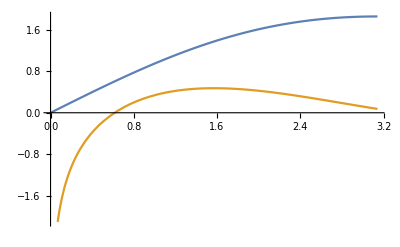

```mathematica
Plot[{SinIntegral[β],CosIntegral[β]},{β,0,π}]
```

## Normalization

Normalize p=p̃ p, r =r̃ l with l=L
So H=H̃ h

```mathematica
fHH:=1/(2 m)(pz^2+(px-1/(2 c)B0 L q Sin[α] f1)^2+1/c^2 q^2 (B0 x Cos[α]+1/2 B0 L Sin[α] f2)^2)
Simplify[(fHH/.fRules)-RHS]==0
```

True

```mathematica
res=Simplify[fHH//.normRules,assums]
```

1/8 h (4 (pxN^2+pzN^2)+4 xN^2 Cos[α]^2-4 f1 pxN Sin[α]+4 f2 xN Cos[α] Sin[α]+(f1^2+f2^2) Sin[α]^2)

```mathematica
HBar:=1/2  ( pzN^2+(pxN-(f1 Sin[α])/2)^2+(xN Cos[α]+(f2 Sin[α])/2)^2)
Assert[Simplify[h HBar-res]==0]
HBar/.notationRules
```

1/2 ((x Cos[α]+1/2 f2 Sin[α])^2+(-1/2 f1 Sin[α]+p_x)^2+p_z^2)

### Asymptotic Hamiltonian near z=0

```mathematica
Simplify@Asymptotic[{f1/2,f2/2}/.fRules/.normRules,{zN,0,3}]/.notationRules
```

{z-(z^3 β^2)/6,-(z^2 β)/2+CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β]}

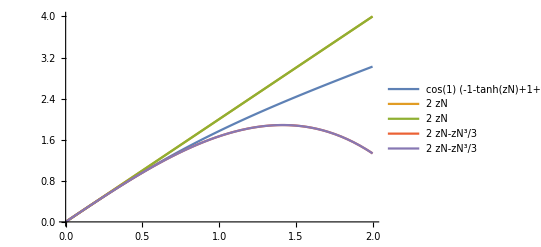

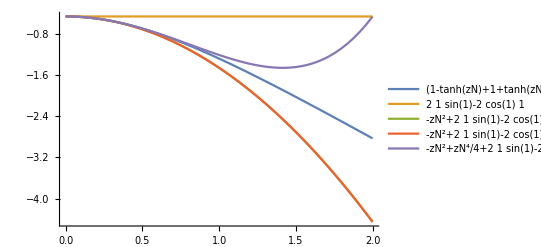

```mathematica
asyPlot[f_,n_:4,βTemp_:1]:=Block[{β=βTemp},
asyfs=Table[Asymptotic[f,{zN,0,i}],{i,n}];
Plot[{f,asyfs}//Evaluate,{zN,0,2},PlotLegends->"Expressions"]
]

asyPlot[f1/.fRules/.normRules]
asyPlot[f2/.fRules/.normRules]
```

## Equations

Thus H̃=1/2 ((x̃ Cos[α]+1/2 f_2 Sin[α])^2+(-1/2 f_1 Sin[α]+OverTilde[p_x])^2+OverTilde[p_z]^2)

```mathematica
f1t:=f1z/.{z/L->z}
f2t:=f2z/.{z/L->z}
H:=HBar/.{xN->x,pzN->pz,pxN->px,f1->f1t,f2->f2t}
Ht:=H/.{x->x[t],z->z[t],px->px[t],pz->pz[t]}
(*H:=1/2 pz[t]^2+1/2(px[t]-1/2 Sin[α]f1t)^2+1/2(Cos[α]x[t]+1/2 Sin[α]f2t)^2;*)
```

```mathematica
hamiltonianEquations:={
px'[t]==-D[Ht, x[t]],
x'[t]==D[Ht, px[t]],
pz'[t]==-D[Ht, z[t]],
z'[t]==D[Ht, pz[t]]
}
```

```mathematica
U:=Simplify[H-1/2 pz^2];
```

```mathematica
eq:={D[U,z]==0,D[U,z]<0,H==1/2/.{pz->0}}
sol:=NSolveValues[
eq,{x,px},Reals
]
```

```mathematica
Block[{α=π/2-0.01,β=π/2},
eq
]
```

{1/2 (2 (-0.785359 Sech[z]^2 Sinc[1/2 π (1+Tanh[z])]-0.785359 Sech[z]^2 Sinc[1/2 (π-π Tanh[z])]) (px-0.499975 SinIntegral[1/2 π (1+Tanh[z])]+0.499975 SinIntegral[1/2 (π-π Tanh[z])])+0.99995 (0.00999983 x+0.499975 (CosIntegral[1/2 π (1+Tanh[z])]+CosIntegral[1/2 (π-π Tanh[z])])) ((Cos[1/2 π (1+Tanh[z])] Sech[z]^2)/(1+Tanh[z])-(π Cos[1/2 (π-π Tanh[z])] Sech[z]^2)/(π-π Tanh[z])))==0,1/2 (2 (-0.785359 Sech[z]^2 Sinc[1/2 π (1+Tanh[z])]-0.785359 Sech[z]^2 Sinc[1/2 (π-π Tanh[z])]) (px-0.499975 SinIntegral[1/2 π (1+Tanh[z])]+0.499975 SinIntegral[1/2 (π-π Tanh[z])])+0.99995 (0.00999983 x+0.499975 (CosIntegral[1/2 π (1+Tanh[z])]+CosIntegral[1/2 (π-π Tanh[z])])) ((Cos[1/2 π (1+Tanh[z])] Sech[z]^2)/(1+Tanh[z])-(π Cos[1/2 (π-π Tanh[z])] Sech[z]^2)/(π-π Tanh[z])))<0,1/2 ((0.00999983 x+0.499975 (CosIntegral[π/2-1/2 π Tanh[z]]+CosIntegral[π/2+1/2 π Tanh[z]]))^2+(px-0.499975 (-SinIntegral[π/2-1/2 π Tanh[z]]+SinIntegral[π/2+1/2 π Tanh[z]]))^2)==1/2}

```mathematica
tempPlot:=Block[{α=π/2-0.01,β=π/2},
sol=NSolveValues[
(D[U, z]==0)&&
(H==1/2)/.{pz->0},{x,px}];
ParametricPlot[sol,{z,-3,3},
PlotLabel->StringForm["c_1: `` c_2: ``",N@c1,N@c2]]
]
```